```mathematica
Cos[β]Sin[α]+Cos[α] √(Sin[β]^2-4 Cos[β]^2 Tan[α](Tan[β]-Tan[α]))/.α->ArcCos[4/7]/.β->ArcCos[4/7]//FullSimplify//N
```

0.937888

```mathematica
Sin[β-α]/.α->ArcCos[4/7]/.β->ArcCos[4/7]//FullSimplify//N
```

0.

```mathematica
√(Sin[β]^2-4 Cos[β]^2 Tan[α](Tan[β]-Tan[α]))/.α->ArcCos[6/7]/.β->ArcCos[3/7]//FullSimplify
```

1/7 √(53-4 √130)

```mathematica
Solve[{y==x Tan[β]-(g x^2)/(2 v^2 Cos[β]^2),y==x Tan[α]},{x,y}]//FullSimplify
```

{{x→0,y→0},{x→-(2 v^2 Cos[β] Sec[α] Sin[α-β])/g,y→-(2 v^2 Cos[β] Sec[α] Sin[α-β] Tan[α])/g}}

```mathematica
{x,y}g/(2 v^2)/.%17[[2]]/.α->ArcCos[6/7]/.β->ArcCos[3/7]//FullSimplify
```

{1/2 Sin[ArcCos[3/7]-ArcCos[6/7]],1/196 (-13+4 √130)}

```mathematica
RootReduce[%21]
```

{Root[729-12456 #1^2+38416 #1^4&,3],1/196 (-13+4 √130)}

```mathematica
%22[[2]]//N
```

0.166362

```mathematica
Cos[α]Cos[β]-√(Sin[β]^2-4 Cos[β]^2 Tan[α](Tan[β]-Tan[α]))Sin[α]/.α->ArcCos[6/7]/.β->ArcCos[3/7]//FullSimplify
```

1/49 (31-2 √130)

```mathematica
N[2/49 (-71+√130)]
```

-2.43258

```mathematica
N[1/49 (31-2 √130)]
```

0.167275

```mathematica
N[1/49 (5+2 √130)]
```

0.567419

```mathematica
pt0=x/.Solve[(x-0.05) Tan[β]-k (x-0.05)^2+0.4 0.95==0.4(1-x)/.β->π/6/.k->1.1,x][[2]]
```

0.9385

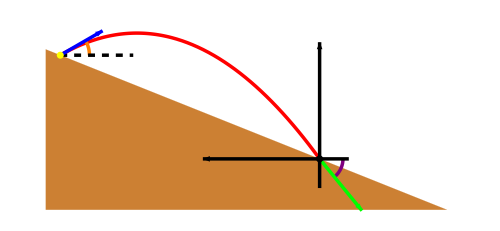

```mathematica
Show[Plot[0.4(1-x),{x,0,1.4},Filling->Bottom,FillingStyle->RGBColor[0.8,0.5,0.2],PlotStyle->{Thickness[0.00],RGBColor[0.8,0.5,0.2]},ImageSize->500,AspectRatio->0.65/1.4,Axes->False,PlotRange->{{0,1.4},{-0.15,0.5}}],Plot[(x-0.05) Tan[β]-k (x-0.05)^2+0.4 0.95/.β->π/6/.k->1.1,{x,0.05,pt0},PlotStyle->{Red,Thickness[0.005]}],Graphics[{Thickness[0.005],Purple,Circle[{pt0,0.4(1-pt0)},0.08,{ArcTan[(pt0-0.05)/(√3)-2 1.1(pt0-0.05)^2],-0.03}],Orange,Circle[{0.050,0.4 0.95},0.1,{0,ArcTan[1.1/2]}]}],Graphics[{Thickness[0.005],Dashed,Line[{{0.05,0.4 0.95},{0.3,0.4 0.95}}]}],Graphics[{Blue,Thickness[0.005],Arrow[{{0.05,0.4 0.95},{0.05+0.145,0.4 0.95+0.145 1/(√3)}}],Green,Arrow[{{pt0,0.4(1-pt0)},{pt0+0.145,0.4(1-pt0)+0.145((pt0-0.05)/(√3)-2 1.1(pt0-0.05)^2)}}]}],Graphics[{Disk[{pt0,0.4(1-pt0)},0.012],Yellow,Disk[{0.05,0.4 0.95},0.012]}],Graphics[{Thickness[0.005],Arrow[{{pt0,0.4(1-pt0)-0.1},{pt0,0.4(1-pt0)+0.4}}],Arrow[{{pt0+0.1,0.4(1-pt0)},{pt0-0.4,0.4(1-pt0)}}]}]]
```

```mathematica
Manipulate[Graphics[{RGBColor[r,g,b],Disk[]}],{r,0,1},{g,0,1},{b,0,1}]
```

```mathematica
Cos[α]Cos[α+β1]+Sin[α]Sin[α+β1]//FullSimplify
```

Cos[β1]

```mathematica
√(Tan[β]^2-4Tan[α](Tan[β]-Tan[α]))/.α->ArcCos[6/7]/.β->ArcCos[3/7]//FullSimplify//N
```

0.906335

```mathematica
Cos[2α]Cos[β]-Sin[2α] √(Sin[β]^2-4 Cos[β]^2 Tan[α](Tan[β]-Tan[α]))/.α->ArcCos[6/7]/.β->ArcSin[3/7]//FullSimplify
```

1/343 (-58 √10+36 √13)

```mathematica
N[1/343 (-58 √10+36 √13)]
```

-0.156304

```mathematica
2ArcCos[6/7]/Degree//N
```

62.0054

```mathematica
ArcTan[√(Tan[β^2]-4Tan[α](Tan[β]-Tan[α]))]/Degree/.α->ArcCos[6/7]/.β->ArcSin[3/7]//N
```

35.3451

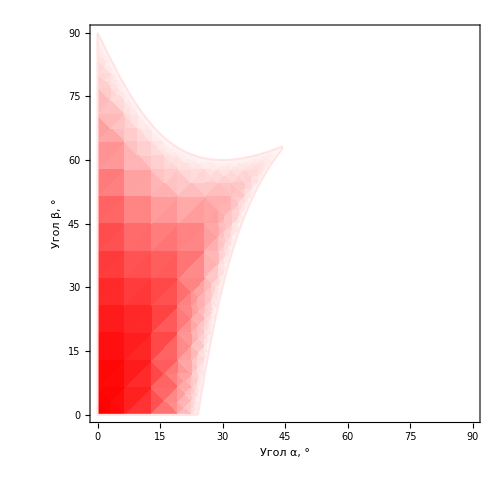

```mathematica
DensityPlot[Cos[2α Degree]Cos[β Degree]-Sin[2α Degree] √(Sin[β Degree]^2-4 Cos[β Degree]^2 Tan[α Degree](Tan[β Degree]-Tan[α Degree])),{α,0,90},{β,0,90},RegionFunction->Function[{α,β},Cos[2α Degree]Cos[β Degree]-Sin[2α Degree]√(Sin[β Degree]^2-4 Cos[β Degree]^2 Tan[α Degree](Tan[β Degree]-Tan[α Degree]))>0],ColorFunction->Function[f,Hue[0,f,1]],BoundaryStyle->{Black,Thickness[0.003]},ImageSize->500,PlotRange->{{0,90},{0,90}},FrameTicks->{{{0,15,30,45,60,75,90},None},{{0,15,30,45,60,75,90},None}},FrameTicksStyle->Directive[24,FontFamily->"Times New Roman"],FrameLabel->{Style["Угол α, °",28,FontFamily->"Times New Roman"],Style["Угол β, °",28,FontFamily->"Times New Roman"]}]
```

```mathematica
Rasterize[%44,ImageResolution->200]
```

-Graphics-